```mathematica
CircleLayout[n_]:=Table[{Cos[2π/n i],Sin[2π/n i]},{i,n}];
AddPath[g_Graph,list_List]:=EdgeAdd[g,Thread[UndirectedEdge[list[[;;-2]],list[[2;;]]]]];
AddCycle[g_Graph,list_List]:=EdgeAdd[g,Thread[UndirectedEdge[list,RotateLeft[list]]]];
```

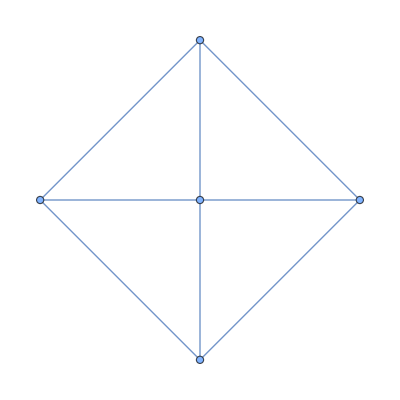

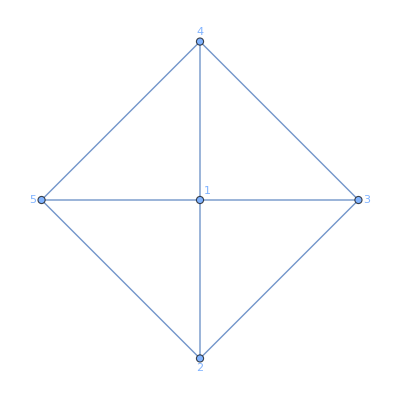

```mathematica
g=AddPath[StarGraph[5],{2,3,4,5,2}]
GraphPlot[g,VertexLabels->"Name"]
```